## 慣性モーメントの計算

```mathematica
ClearAll["Global`*"];
(*integrate{r^2 dmass}*)
(*ρ*integrate{r^2 dv}*)
(*integrate{r^2 dmass}*)
(*正しいとする値*)
rhoPMMA=(1.18(*g/cm^3*))/1000/0.01^3(*kg/cm^3*)
Lx=0.3;(*m*)
Ly=0.42;(*m*)
Lz=0.2;(*m*)
draught=0.1;
rhoBody=500;
massBody=rhoBody*Lx*Ly*Lz;

distanceFromAxis[X_,O_,axis_]:=X-O-Dot[X-O,Normalize[axis]]*Normalize[axis];
volume[d_]:=Integrate[1,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]-Integrate[1,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}];
ans=Solve[rhoPMMA*volume[d]==massBody&&d<Lx/2&&d<Ly/2&&d<Lz/2,d,Reals];
d=d/.ans[[1]](*計算した板厚*);
Print["計算した板厚:",d]
```

1180.

計算した板厚:0.0232806

```mathematica
MOI[axis_]:=rhoPMMA*FullSimplify[
Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2,Lx/2},{y,-Ly/2,Ly/2},{z,-Lz/2,Lz/2}]
-Integrate[
Dot[distanceFromAxis[{x,y,z},{0,0,0},axis],distanceFromAxis[{x,y,z},{0,0,0},axis]]
,{x,-Lx/2+d,Lx/2-d},{y,-Ly/2+d,Ly/2-d},{z,-Lz/2+d,Lz/2-d}]
]
Print["計算した厚さに基づく結果，{Ixx,Iyy,Izz}=",{MOI[{1,0,0}],MOI[{0,1,0}],MOI[{0,0,1}]}]

Print["密度が均一とした場合:",
{1/12*rhoBody*Lx*Ly*Lz*(Ly*Ly+Lz*Lz),
1/12*rhoBody*Lx*Ly*Lz*(Lx*Lx+Lz*Lz),
1/12*rhoBody*Lx*Ly*Lz*(Lx*Lx+Ly*Ly)}
]
```

計算した厚さに基づく結果，{Ixx,Iyy,Izz}={0.303475,0.196798,0.369273}

密度が均一とした場合:{0.22722,0.1365,0.27972}

## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]

(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
(*data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
*)

(*ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
name="/Volumes/home/BEM/流体力学会2023/Ren2015_H0d04_T1d2_potential_2/result.json"*)

ExperimentData=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d1_T1d2.csv"];
ExperimentData0d04=Import[NotebookDirectory[]<>"Ren2015_Fig14_H0d04_T1d2.csv"];
ExperimentData0d04Heave=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_heave.csv"];
ExperimentData0d04Surge=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_surge.csv"];
ExperimentData0d04Pitch=Import[NotebookDirectory[]<>"Ren2015_Fig11_H0d04_T1d2_pitch.csv"];
name="/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json"
name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_piston_positive/result.json";
(*name="/Users/tomoaki/BEM/Li_Cheng2018meshB_H0d04_T1d2_piston_positive/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_flap/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential/result.json"*)
(*name="/Users/tomoaki/BEM/Li_Cheng2018_H0d04_T1d2_potential_pahse_shift/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_positive_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_piston_2_negative_start_long/result.json"*)
(*name="/Users/tomoaki/BEM/Ren2015_H0d04_T1d2_potential_2/result.json"*)
```

plot2Doption

/Volumes/home/BEM/20230922流体力学会年会東京農業大学/Ren2015_H0d04_T1d2_potential_2/result.json

```mathematica
imported=Import[name];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
importGetData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
jsonInfo[name_]:=With[{imported=Import[name,"JSON"]},Grid[Join[{{"no.","title","length"}},Table[{i,imported[[i]][[1]],Length[imported[[i]][[2]]]},{i,1,Min[10,Length[imported]]}]],Frame->All,Background->{None,{LightGray,{LightGreen,Green}}}]]
jsonInfo[name]
```

no. | title | length
1 | cpu_time | 701
2 | float_COM | 701
3 | float_EK | 701
4 | float_EP | 701
5 | float_accel | 701
6 | float_area | 701
7 | float_force | 701
8 | float_pitch | 701
9 | float_roll | 701
10 | float_torque | 701

```mathematica
legend=LineLegend[{"mesh A","mesh B","mesh C","mesh D","mesh E","Exp (Ren et al., 2015)"},LegendMarkerSize->20,LabelStyle->10];
plotstyle={{Red,Dashed},{Blue},{Green,Dashed},{Orange},{Magenta},{Black}};
h=0.4;
d=0.1;
H=0.04;
T=1.2;

w=2π/T;
g=9.81;
Clear[k];
NSolve[w^2==g*k*Tanh[h*k],k,Reals];
k=Abs[k/.%[[1]]]

shift=1.95;
```

3.24503

## ALEが計算結果に与える影響

```mathematica
(*メッシュが細かくなるに従って，計算結果が収束することを期待していた．しかし，波の運動は早く収束するのだが，浮体の運動は直線的に収束しているようには見えなかった．
浮体周辺のメッシュの細かさが影響するだろうと考え計算したところ，浮体の運動は確かに大きく変化したが，期待する収束方向に変化しなかった．
メッシュの細かさはALEによる修正度合いにも影響を与えるだろうから，これまで確認したメッシュと計算の関係は，実はALEと計算の関係が根本的には決めているのではないかと考えた．
そこで，ALEを適用する頻度N，N time_stepに1度，を変更して計算結果を比較してみる．

ALEはできるだけ少ない方が収束しやすい，のような結果が得られるのではないか．

結果：ALEの頻度は，結果に影響を及ぼさなかった．
慣性モーメントが正しくないためにこのような結果になったと考えられる．
*)
```

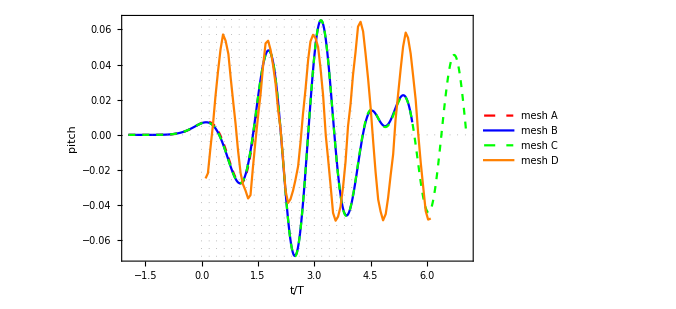

```mathematica
meshAALE1="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_potential_ALE1/result.json";
meshAALE3="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE3/result.json";
meshAALE6="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_piston_positive_ALE6/result.json";
ListPlot[
{{importGetData[meshAALE1,"simulation_time"]-shift,(importGetData[meshAALE1,"float_pitch"])}ᵀ,
{importGetData[meshAALE3,"simulation_time"]-shift,(importGetData[meshAALE3,"float_pitch"])}ᵀ,
{importGetData[meshAALE6,"simulation_time"]-shift,(importGetData[meshAALE6,"float_pitch"])}ᵀ,
{T*#1+0.1,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True,True,True,True},
PlotStyle->plotstyle,
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

## メッシュの細かさが計算結果に与える影響

```mathematica
(*メッシュと計算の収束*)
meshA="/Users/tomoaki/BEM/Cheng2018meshA_H0d04_T1d2_potential_ALE1/result.json";
meshB="/Users/tomoaki/BEM/Cheng2018meshB_H0d04_T1d2_piston_positive/result.json";
meshC="/Users/tomoaki/BEM/Cheng2018meshC_H0d04_T1d2_potential_ALE1/result.json";
meshD="/Users/tomoaki/BEM/Cheng2018meshD_H0d04_T1d2_piston_positive_ALE1/result.json";
meshE="/Users/tomoaki/BEM/Cheng2018meshF_H0d04_T1d2_piston_positive_ALE1/result.json";
Dimensions["cpu_time"/.Import[meshA]]
Dimensions["cpu_time"/.Import[meshB]]
Dimensions["cpu_time"/.Import[meshC]]
Dimensions["cpu_time"/.Import[meshD]]
Dimensions["cpu_time"/.Import[meshE]]
```

{359}

{149}

{1251}

{1517}

{1848}

```mathematica
Manipulate[
ListPlot[
{{importGetData[meshA,"float_COM",1]-shift,importGetData[meshA,"float_COM",3]-0.4}ᵀ,
{importGetData[meshB,"float_COM",1]-shift,importGetData[meshB,"float_COM",3]-0.4}ᵀ,
{importGetData[meshC,"float_COM",1]-shift,importGetData[meshC,"float_COM",3]-0.4}ᵀ,
{importGetData[meshD,"float_COM",1]-shift,importGetData[meshD,"float_COM",3]-0.4}ᵀ,
{importGetData[meshE,"float_COM",1]-shift,importGetData[meshE,"float_COM",3]-0.4}ᵀ,
{#1,#2}&@@@ExperimentData0d04},
PlotRange->{{-0.04,0.04},Automatic},
Joined->{True,True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
],{shift,3.3398,3.5}]
```

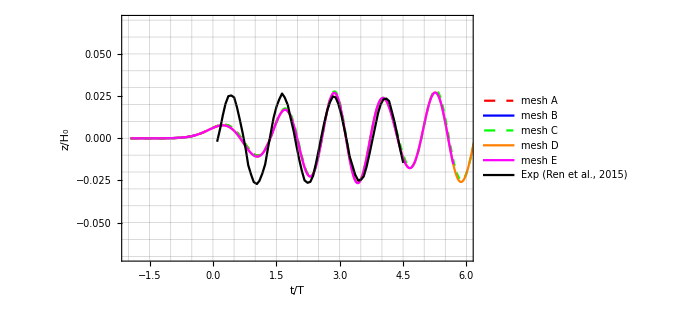

```mathematica
fig=ListPlot[
{{(importGetData[meshA,"simulation_time"])-shift,(importGetData[meshA,"float_COM",3]-0.4)}ᵀ,
{(importGetData[meshB,"simulation_time"])-shift,(importGetData[meshB,"float_COM",3]-0.4)}ᵀ,
{(importGetData[meshC,"simulation_time"])-shift,(importGetData[meshC,"float_COM",3]-0.4)}ᵀ,
{(importGetData[meshD,"simulation_time"])-shift,(importGetData[meshD,"float_COM",3]-0.4)}ᵀ,
{(importGetData[meshE,"simulation_time"])-shift,(importGetData[meshE,"float_COM",3]-0.4)}ᵀ,
{T*#1+0.1,h#2}&@@@ExperimentData0d04Heave},
Joined->{True,True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{{-2,6.},{-0.07,0.07}},
(*PlotRange->{Automatic,Automatic},*)
GridLines->All(*{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]}*),
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
Evaluate[plot2Doption]
]
```

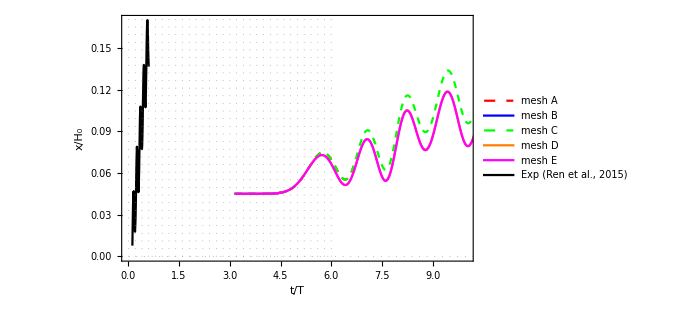

```mathematica
ListPlot[
{{importGetData[meshA,"simulation_time"]-shift,(importGetData[meshA,"float_COM",1]-3.305)}ᵀ,
{importGetData[meshB,"simulation_time"]-shift,(importGetData[meshB,"float_COM",1]-3.305)}ᵀ,
{importGetData[meshC,"simulation_time"]-shift,(importGetData[meshC,"float_COM",1]-3.305)}ᵀ,
{importGetData[meshD,"simulation_time"]-shift,(importGetData[meshD,"float_COM",1]-3.305)}ᵀ,
{importGetData[meshE,"simulation_time"]-shift,(importGetData[meshE,"float_COM",1]-3.305)}ᵀ,
{T*#1+0.1,h#2}&@@@ExperimentData0d04Surge},
Joined->{True,True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{{0,10.},Automatic},
(*PlotRange->{Automatic,Automatic},*)
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->legend,
GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->legend,
Evaluate[plot2Doption]
]
```

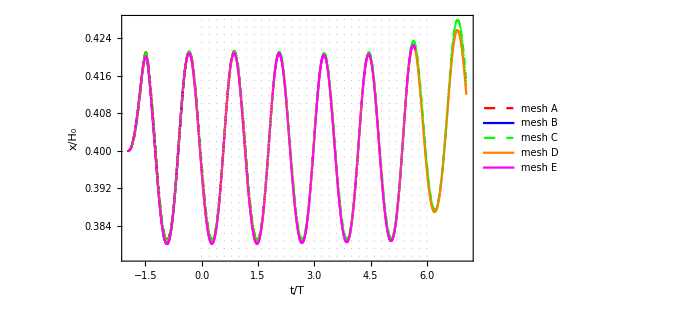
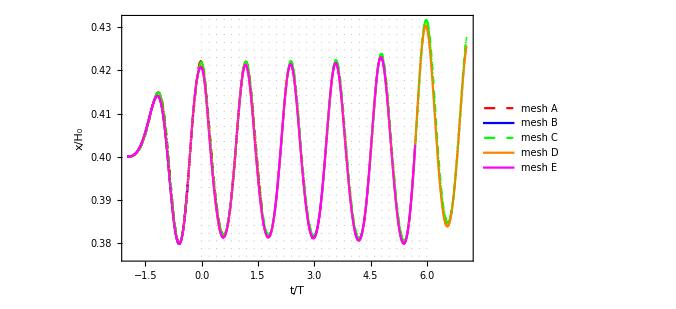
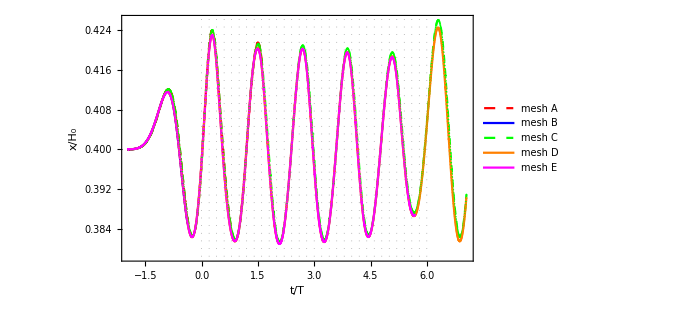
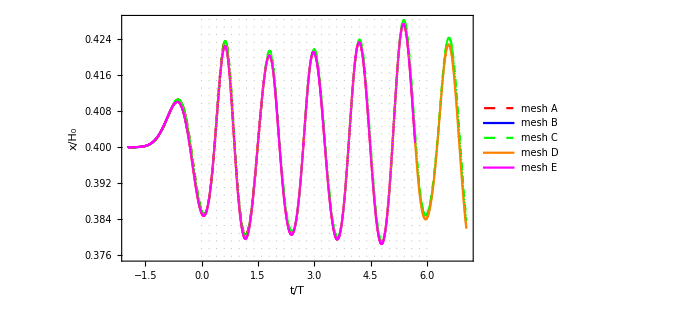

```mathematica
Table[
ListPlot[
{{importGetData[meshA,"simulation_time"]-shift,(importGetData[meshA,data,3])}ᵀ,
{importGetData[meshB,"simulation_time"]-shift,(importGetData[meshB,data,3])}ᵀ,
{importGetData[meshC,"simulation_time"]-shift,(importGetData[meshC,data,3])}ᵀ,
{importGetData[meshD,"simulation_time"]-shift,(importGetData[meshD,data,3])}ᵀ,
{importGetData[meshE,"simulation_time"]-shift,(importGetData[meshE,data,3])}ᵀ},
Joined->{True,True,True,True,True},
PlotStyle->plotstyle,
Mesh->All,
PlotRange->{All,All},
(*PlotRange->{Automatic,Automatic},*)
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,7.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->legend,
Evaluate[plot2Doption]
],{data,{"gauge0_intersection","gauge1_intersection","gauge2_intersection","gauge3_intersection"}}]
```

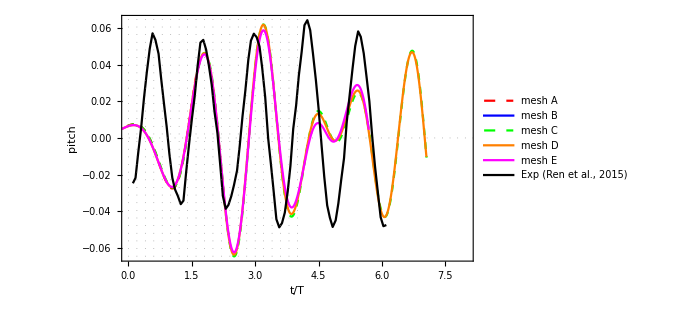

```mathematica
ListPlot[
{{importGetData[meshA,"simulation_time"]-shift,(importGetData[meshA,"float_pitch"])}ᵀ,
{importGetData[meshB,"simulation_time"]-shift,(importGetData[meshB,"float_pitch"])}ᵀ,
{importGetData[meshC,"simulation_time"]-shift,(importGetData[meshC,"float_pitch"])}ᵀ,
{importGetData[meshD,"simulation_time"]-shift,(importGetData[meshD,"float_pitch"])}ᵀ,
{importGetData[meshE,"simulation_time"]-shift,(importGetData[meshE,"float_pitch"])}ᵀ,
{T*#1+0.1,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True,True,True,True},
PlotStyle->plotstyle,
PlotRange->{{0,8.},All},
PlotRange->{Automatic,Automatic},
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["pitch",FontSize->20,FontFamily->"Times"]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

```mathematica
Manipulate[
ListPlot[
{{getData["float_COM",1]-shift,getData["float_COM",3]-0.4}ᵀ
(*,{#1,#2}&@@@ExperimentData,*)
,{#1,#2}&@@@ExperimentData0d04},
PlotRange->All,
Joined->{True,True,False},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{Automatic,Automatic},
PlotLabel->shift,
FrameLabel->{Style["x",FontSize->20,FontFamily->"Times",Italic],Style["y",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
],{shift,3.3882,3.5}]
```

```mathematica
plotxrange={-1,6};
```

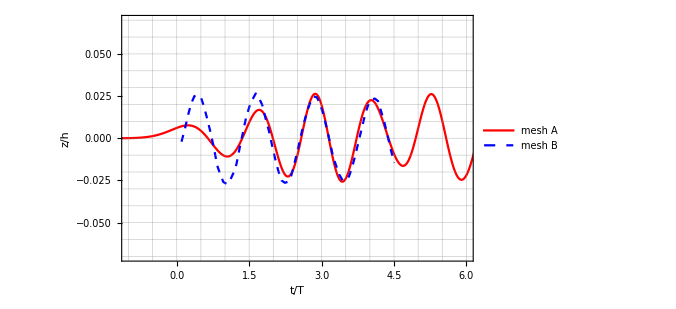

```mathematica
fig=ListPlot[
{{(getData["simulation_time"])-shift,(getData["float_COM",3]-0.4)}ᵀ,
{T*#1+0.1,h#2}&@@@ExperimentData0d04Heave},
Joined->{True,True},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{plotxrange,{-0.07,0.07}},
(*PlotRange->{Automatic,Automatic},*)
GridLines->All(*{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]}*),
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/h",FontSize->20,FontFamily->"Times",Italic]},
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

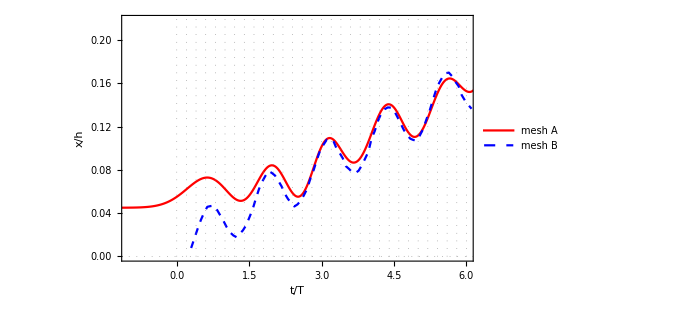

```mathematica
ListPlot[
{{getData["simulation_time"]-shift,(getData["float_COM",1]-3.305)}ᵀ,
{T*#1+0.1,h*#2}&@@@ExperimentData0d04Surge},
Joined->{True,True},
PlotStyle->{{Red},{Blue,Dashed}},
PlotRange->{plotxrange,Automatic},
(*PlotRange->{Automatic,Automatic},*)
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/h",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,7.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

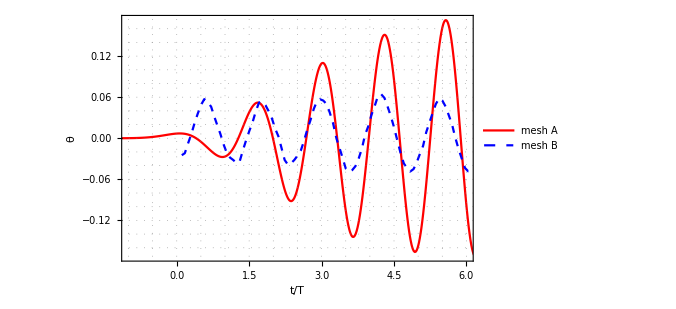

```mathematica
ListPlot[
{{getData["simulation_time"]-shift,getData["float_pitch"]}ᵀ,
{T*#1+0.1,k*h#2}&@@@ExperimentData0d04Pitch},
Joined->{True,True},
PlotStyle->{{Red},{Blue,Dashed}},
(*PlotRange->{{0,2.},{-1.,1.}},*)
PlotRange->{plotxrange,Automatic},
GridLines->All,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ",FontSize->20,FontFamily->"Times"]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

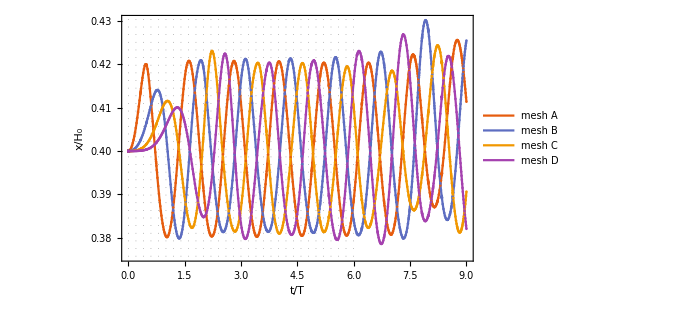

```mathematica
ListPlot[
{{getData["simulation_time"],(getData["gauge0_intersection",3])}ᵀ,
{getData["simulation_time"]-1*0.,(getData["gauge1_intersection",3])}ᵀ,
{getData["simulation_time"]-2*0.,(getData["gauge2_intersection",3])}ᵀ,
{getData["simulation_time"]-3*0.,(getData["gauge3_intersection",3])}ᵀ},
Joined->{True,True},
(*PlotStyle->{{Red},{Blue,Dashed}},*)
Mesh->All,
PlotRange->{All,All},
(*PlotRange->{Automatic,Automatic},*)
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,7.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
PlotLegends->Placed[legend,{0.65,0.15}],
Evaluate[plot2Doption]
]
```

1/2 (1-Tanh[2.35619-20 π x])

-π

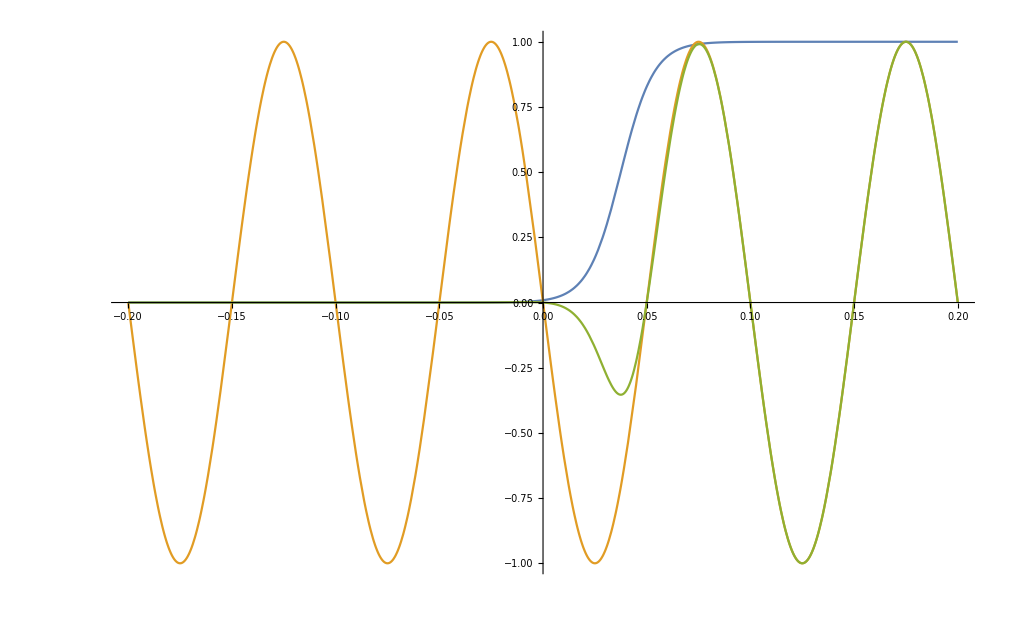

```mathematica
T=1/10;
f[x_]:=((Tanh[2Pi*x/T-0.75Pi]+1)/2);
FullSimplify@f[x]
shift=-Pi
Plot[{f[x],Sin[2Pi*x/T+shift],f[x]*Sin[2Pi*x/T+shift]},{x,-2T,2T}]
```

```mathematica
.00.00
```